```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

## Eingabe (𝒹𝒶𝓉ℯ𝓃)

```mathematica
ClearAll["Global`*"]
𝒹𝒶𝓉ℯ𝓃=({{0.024445375343834175, 0.31867819235031736}, {0.018061915873975192, 0.0646319983475846}, {0.0448172586448251, 0.25864096889235766}, {0.053059192027113095, 0.29607509780242147}, {0.0931429297254965, 0.37704937076853695}, {0.06950795694097277, 0.5580731001358521}, {0.12508046239233367, 0.5048171710077578}, {0.1480099303951074, 0.5869239472192351}, {0.20083324831215452, 0.7360454435393655}, {0.17155017597136002, 0.7430377835718397}, {0.19118719260954162, 0.7926165472961512}, {0.24468354110929685, 1.2343110238848705}, {0.2750130038781702, 1.2057846325708226}, {0.26903769140911915, 1.0179210309119564}, {0.23138019563303197, 0.8189751038319326}, {0.34556221402134796, 1.2675965128207447}, {0.3423977420911196, 1.2451250448016769}, {0.3827382785499513, 1.5554382950720331}, {0.3635295541719923, 1.324773903624557}, {0.3887241780342249, 1.363784075384805}, {0.39564507402950544, 1.5134533608600063}, {0.40270570922859616, 1.2496320293282888}, {0.45055583469370236, 1.3124703939853193}, {0.45178294580248723, 1.4321498352766815}, {0.4401845794770551, 1.6188409824291252}, {0.5448873509958516, 1.6982689023239692}, {0.4707750780903462, 1.6147314679666016}, {0.5639093453783948, 1.669512879519247}, {0.5659040098219058, 1.6051062469981527}, {0.5437892275100311, 1.7523236891393372}, {0.569627805443411, 1.5093488989910508}, {0.6408291446789397, 1.8267519810214183}, {0.6278451228052516, 1.882403793412942}, {0.6381900916963406, 1.8256555701870174}, {0.653404304461709, 1.6808190977016673}, {0.7112655107259417, 1.7447095922981726}, {0.7622720652636688, 1.9085483125214517}, {0.7222773094592356, 1.8339867989588297}, {0.7734446927011259, 1.677485252922632}, {0.8214726726992679, 1.8321890442661268}, {0.847234207159934, 1.9155555355480387}, {0.8220304423851439, 1.9677009625388517}, {0.8439223677946734, 2.0089176037843997}, {0.8978892052389247, 1.8855474639933782}, {0.905312550745709, 1.9264691356644694}, {0.8970502030169579, 1.7283535755529864}, {0.9177526260330685, 1.759650302479884}, {0.9261864897034173, 1.9148901364194728}, {1.0011969361458803, 1.8772167726900508}, {0.9901309223017096, 2.0152057780356576}, {0.9976929176328178, 1.767355439914713}});
```

## Plot

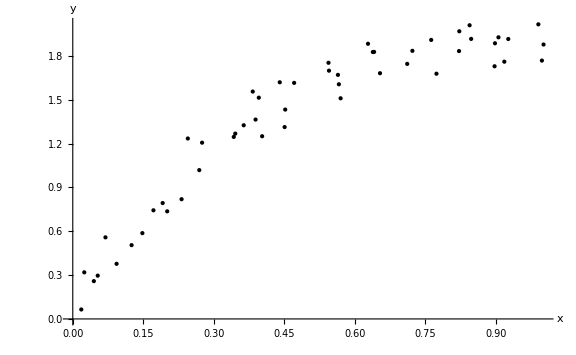

```mathematica
plotDaten=ListPlot[𝒹𝒶𝓉ℯ𝓃,
PlotStyle->{Black,PointSize->Medium},AxesLabel->{"x","y"},PlotRange->All,ImageSize->Large];
Print[Show[plotDaten]]
```

## Programm (automatisch)

```mathematica
𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃={
a-b(x-c)^2,
a+b Sin[c x],
a-b ⅇ^(-c x),
a+b x+c x^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={a,b,c,d,e,f};
```

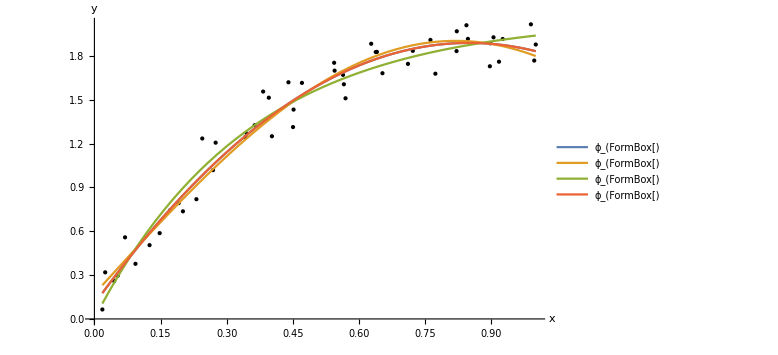

ϕ(x) = (1.88811-2.47356 (-0.849839+x)^2
0.170701+1.73127 Sin[1.91662 x]
2.05832-2.05588 ⅇ^(-2.83791 x)
0.101638+4.20426 x-2.47356 x^2)

```mathematica
(*Programm*)
ϕ=Table[
𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃[[i]]/.FindFit[𝒹𝒶𝓉ℯ𝓃,𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃[[i]],𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,x],
{i,Length[𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃]}];

(*Ausgabe*)
plot=Plot[Evaluate[ϕ],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},
PlotRange->All,PlotLegends->Table[StringForm["ϕ_(``)",i],{i,Length[𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃]}]];
Print[Show[plotDaten,plot]]
Print[StringForm["ϕ(x) = ``\n",ϕ//MatrixForm]]
```